## Notebook for Homework 1

#### Get the Data

This is the location of the data on an Excel file:

```mathematica
originalFile="/Users/jaimebuitrago/Dropbox/Jaime/Wolfram Summer School/Boston2017Hourly.xlsx";
```

```mathematica
originalFile2 = "/Users/jaimebuitrago/Dropbox/Jaime/Wolfram Summer School/EnergyJuneMA.xlsx"
```

We need to import the data into a variable and then cleanup

```mathematica
sheet=First@Import[originalFile]
```

{{DateHour,Actual},{Sun 1 Jan 2017 00:00:00GMT-4.,1542.56},{Sun 1 Jan 2017 01:00:00GMT-4.,1436.88},{Sun 1 Jan 2017 01:59:59GMT-4.,1401.3},{Sun 1 Jan 2017 02:59:59GMT-4.,1433.75},{Sun 1 Jan 2017 03:59:59GMT-4.,1384.62},8748,{Sun 31 Dec 2017 16:59:16GMT-4.,2588.58},{Sun 31 Dec 2017 17:59:16GMT-4.,2490.11},{Sun 31 Dec 2017 18:59:16GMT-4.,2404.78},{Sun 31 Dec 2017 19:59:16GMT-4.,2293.56},{Sun 31 Dec 2017 20:59:16GMT-4.,2178.72},{Sun 31 Dec 2017 21:59:16GMT-4.,1769.91}}
 |  |  |  |

```mathematica
headers=First@sheet
```

{DateHour,Actual}

```mathematica
data=Map[AssociationThread[headers->#]&,Rest@sheet]
```

{<|DateHour→Sun 1 Jan 2017 00:00:00GMT-4.,Actual→1542.56|>,<|DateHour→Sun 1 Jan 2017 01:00:00GMT-4.,Actual→1436.88|>,<|DateHour→Sun 1 Jan 2017 01:59:59GMT-4.,Actual→1401.3|>,<|DateHour→Sun 1 Jan 2017 02:59:59GMT-4.,Actual→1433.75|>,8751,<|DateHour→Sun 31 Dec 2017 18:59:16GMT-4.,Actual→2404.78|>,<|DateHour→Sun 31 Dec 2017 19:59:16GMT-4.,Actual→2293.56|>,<|DateHour→Sun 31 Dec 2017 20:59:16GMT-4.,Actual→2178.72|>,<|DateHour→Sun 31 Dec 2017 21:59:16GMT-4.,Actual→1769.91|>}
 |  |  |  |

```mathematica
data1=Rule@@@data[[All,{"DateHour","Actual"}]]
```

{Sun 1 Jan 2017 00:00:00GMT-4.→1542.56,Sun 1 Jan 2017 01:00:00GMT-4.→1436.88,Sun 1 Jan 2017 01:59:59GMT-4.→1401.3,Sun 1 Jan 2017 02:59:59GMT-4.→1433.75,Sun 1 Jan 2017 03:59:59GMT-4.→1384.62,Sun 1 Jan 2017 04:59:59GMT-4.→1458.61,8747,Sun 31 Dec 2017 16:59:16GMT-4.→2588.58,Sun 31 Dec 2017 17:59:16GMT-4.→2490.11,Sun 31 Dec 2017 18:59:16GMT-4.→2404.78,Sun 31 Dec 2017 19:59:16GMT-4.→2293.56,Sun 31 Dec 2017 20:59:16GMT-4.→2178.72,Sun 31 Dec 2017 21:59:16GMT-4.→1769.91}
 |  |  |  |

I want to use the first 14 days of the month for training, therefore I have to cut the dataset to only the first 9 months = 6554 hours

```mathematica
trainingset=data1[[1;;6553]]
```

{Sun 1 Jan 2017 00:00:00GMT-4.→1542.56,Sun 1 Jan 2017 01:00:00GMT-4.→1436.88,Sun 1 Jan 2017 01:59:59GMT-4.→1401.3,Sun 1 Jan 2017 02:59:59GMT-4.→1433.75,Sun 1 Jan 2017 03:59:59GMT-4.→1384.62,Sun 1 Jan 2017 04:59:59GMT-4.→1458.61,6541,Sat 30 Sep 2017 18:59:27GMT-4.→2240.33,Sat 30 Sep 2017 19:59:27GMT-4.→2137.47,Sat 30 Sep 2017 20:59:27GMT-4.→1996.58,Sat 30 Sep 2017 21:59:27GMT-4.→1842.33,Sat 30 Sep 2017 22:59:27GMT-4.→1712.82,Sat 30 Sep 2017 23:59:27GMT-4.→1620.39}
 |  |  |  |

```mathematica
validationset = data1[[337;; 337+23]];
```

{Sun 1 Jan 2017 00:00:00GMT-4.→1542.56,Sun 1 Jan 2017 01:00:00GMT-4.→1436.88,Sun 1 Jan 2017 01:59:59GMT-4.→1401.3,Sun 1 Jan 2017 02:59:59GMT-4.→1433.75,Sun 1 Jan 2017 03:59:59GMT-4.→1384.62,Sun 1 Jan 2017 04:59:59GMT-4.→1458.61,6488,Thu 28 Sep 2017 13:59:27GMT-4.→2662.56,Thu 28 Sep 2017 14:59:27GMT-4.→2654.8,Thu 28 Sep 2017 15:59:27GMT-4.→2589.94,Thu 28 Sep 2017 16:59:27GMT-4.→2427.97,Thu 28 Sep 2017 17:59:27GMT-4.→2395.89,Thu 28 Sep 2017 18:59:27GMT-4.→2240.4}
 |  |  |  |

#### Train a Neural Network

```mathematica
p = Predict[trainingset,Method->"GaussianProcess"]
```

PredictorFunction[…]

We test the network and see how it predicts for the next 24 hours

```mathematica
test = Table[DateObject[{2018, 6, 15, i, 0, 0.}], {i, 0, 24}];
```

```mathematica
forecast = p[test]
```

{1703.9,1705.65,1710.37,1716.73,1723.2,1728.64,1732.55,1734.99,1736.32,1736.97,1737.25,1737.36,1737.41,1737.41,1737.41,1737.41,1737.41,1737.41,1737.41,1737.41,1737.41,1737.41,1737.41,1737.41,1737.41}

```mathematica
actual = validationset[[All, 2]];
```

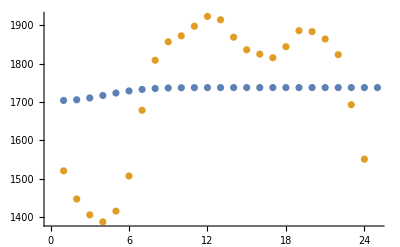

```mathematica
ListPlot[{forecast,actual}]
```